## Bounds on EDGB Theory From the Overall Posterior of GW151226

```mathematica
dataOverall1=Import[NotebookDirectory[]<>"/overall_post.csv","CSV"] ;(*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
dataOverall2=Import[NotebookDirectory[]<>"/-1pn-all-beta.csv","CSV"] ; (*PPE beta*)
dataOverall3=Import[NotebookDirectory[]<>"/-1pn-all-alpha.csv","CSV"] ;(*PPE alpha*)
```

```mathematica
χ1All=dataOverall1[[All,7]]; (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]];
```

```mathematica
m1All=dataOverall1[[All,5]]*tsolar/.tsolar->4.925491*10^-6;
m2All=dataOverall1[[All,6]]*tsolar/.tsolar->4.925491*10^-6;
```

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=1/1.64485*dataOverall2[[All,1]];(*1-sigma upper bound*)
αppEAll=1/1.64485*dataOverall3[[All,1]](*1-sigma upper bound*);
```

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
s2All=2/χ2All^2*(√(1-χ2All^2)-1+χ2All^2);
```

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] ;(*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*);
```

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll]; (*Sigma_Zeta from amplitude corrections*)
```

```mathematica
Length[m1All]
```

52252

```mathematica
Length[βppEAll]
```

52252

```mathematica
Mean[ζampAll]
```

12509.6

```mathematica
Mean[ζphaseAll]
```

360.999

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

51355

```mathematica
Length[ζAllampSelected]
```

46872

```mathematica
Mean[ζAllphaseSelected]
```

0.0174016

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.074786

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219},52250,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193851}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},52250,{0.795965,311.364,3.41712,-0.0397626,4,0.401218,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] (*Data satisfying zeta_phase<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195},51353,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816}}
 |  |  |  |

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},46870,{0.795965,311.364,3.41712,-0.0397626,4,0.401218,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A4[[All,12]]
```

{0.0171763,0.0522075,0.165549,0.0378357,0.0127864,0.0533918,0.0167203,46858,0.0140803,0.0231292,0.000514475,0.0374042,0.727602,0.0315771,0.0686092}
 |  |  |  |

```mathematica
Length[A3]
```

51355

```mathematica
Length[A4]
```

46872

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.094265

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{4.81405,13.8985,6.13673,8.01727,12.5915,5.6388,4.50492,6.70477,52236,4.92185,5.14987,5.2601,2.76716,5.66867,11.4363,5.42432,6.42844}
 |  |  |  |

{2.015,5.74447,2.52291,3.29495,5.19042,2.31966,1.90965,2.94321,52236,2.05282,2.37185,2.2705,1.32689,2.36852,4.71202,2.23658,2.63558}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

7.87527

```mathematica
Mean[SqrtαEDGBphase]
```

3.31329

```mathematica
tsolar=4.925491*10^-6
```

4.92549×10^-6

```mathematica
SqrtαEDGBphaseSelected=((A4[[All,11]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha_EDGB from phase correction of the data satisfying zeta_phase<1*)
```

{2.015,2.52291,3.29495,2.31966,1.90965,2.94321,2.04561,1.98368,46856,2.05282,2.37185,2.2705,1.32689,2.36852,4.71202,2.23658,2.63558}
 |  |  |  |

```mathematica
SqrtαEDGBampSelected=((A4[[All,12]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha from amplitude correction of the data satisfying zeta_amp<1*)
```

{4.81405,6.13673,8.01727,5.6388,4.50492,6.70477,4.82258,4.70667,46856,4.92185,5.14987,5.2601,2.76716,5.66867,11.4363,5.42432,6.42844}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBphaseSelected]
```

2.47235

```mathematica
Mean[SqrtαEDGBampSelected]
```

5.82508

(α^2)_EDGB from phase correction:

```mathematica
LogSquaredαPhase=Log[SqrtαEDGBphase^4] (*This is Log of sigma_(alpha^2)*)
```

{2.80248,6.99295,3.70165,4.76956,6.58725,3.36568,2.58768,4.31801,52236,2.87685,3.45468,3.28,1.13134,3.44905,6.20047,3.21978,3.87642}
 |  |  |  |

```mathematica
Max[LogSquaredαPhase]
```

26.0516

```mathematica
Min[LogSquaredαPhase]
```

0.0172873

```mathematica
𝒟logα=HistogramDistribution[LogSquaredαPhase] ;
```

```mathematica
pslogαPhase=PDF[𝒟logα,x];
```

```mathematica
Histogram[LogSquaredαPhase];
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLog=Prepend[10^Range[-6,11,0.1],0];(*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

```mathematica
fun1αphaseTable[y_]=Table[{αSampleLog[[i]],fun1αphase[αSampleLog[[i]],y]},{i,1,Length[αSampleLog]}]; (*Table for fun1αphase*)
```

```mathematica
αPhaseMC[x_]=pslogαPhase;
```

```mathematica
αPhaseMC[-0.25]
```

0.

```mathematica
αPhaseMC[27]
```

0.

```mathematica
αMCSample=Range[-0.25,27,0.5];
```

```mathematica
αMCTable=Table[{αMCSample[[i]],αPhaseMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];
```

```mathematica
αMCTableInterp=Interpolation[αMCTable];
```

```mathematica
plotαMCTableInterp=Plot[αMCTableInterp[x],{x,-0.25,27},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All];
```

```mathematica
plot5=Plot[αPhaseMC[x],{x,-0.25,27},Filling->Axis,PlotStyle->Gray,PlotRange->All];
```

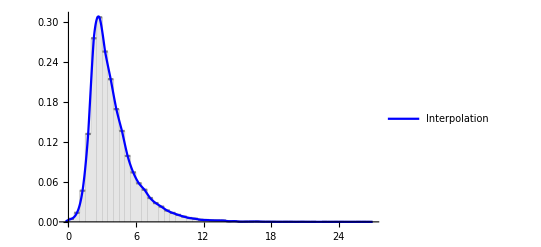

```mathematica
Show[plot5,plotαMCTableInterp] (*Interpolation matches the actual pdf of monte-carlo*)
```

```mathematica
αFinalPDFPhaseLog=Table[{fun1αphaseTable[y][[i,1]],NIntegrate[fun1αphaseTable[y][[i,2]]αMCTableInterp[y],{y,-0.25,27}]},{i,1,Length[fun1αphaseTable[y]]}];
```

```mathematica
αFinalPDFPhaseInterpLog=Interpolation[αFinalPDFPhaseLog];
```

```mathematica
αNormalization=NIntegrate[αFinalPDFPhaseInterpLog[x],{x,0,10^11}]
```

0.499714

```mathematica
αFinalPDFPhaseLogNorm=Table[{αFinalPDFPhaseLog[[i,1]],αFinalPDFPhaseLog[[i,2]]/αNormalization},{i,1,Length[αFinalPDFPhaseLog]}];
```

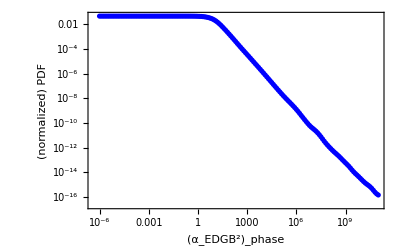

```mathematica
plotαFinalPDFPhaseLogNorm=ListLogLogPlot[{αFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFPhaseInterpLogNorm=Interpolation[αFinalPDFPhaseLogNorm];
```

```mathematica
αFinalCDFPhaseNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFPhaseInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}];
```

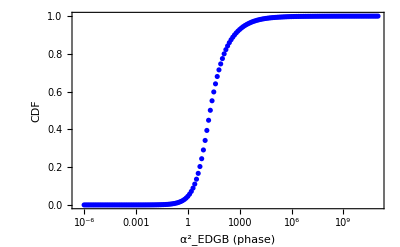

```mathematica
ListLogLinearPlot[αFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (phase)","CDF"}]
```

```mathematica
αFinalCDFPhaseNormInterp=Interpolation[αFinalCDFPhaseNorm];
```

```mathematica
αSquared90CLphase=x/.FindRoot[αFinalCDFPhaseNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

496.956

```mathematica
√√αSquared90CLphase//N
```

4.72149

```mathematica
4.720526510106356
```

4.72053

```mathematica
Subscript[α^2, EDGB] from amplitude correction:
```

```mathematica
LogSquaredαamp=Log[SqrtαEDGBamp^4]
```

{6.28615,10.5271,7.25717,8.32639,10.1321,6.91868,6.02068,7.61128,52236,6.37474,6.55588,6.6406,4.07129,6.93982,9.74718,6.76357,7.44293}
 |  |  |  |

```mathematica
Max[LogSquaredαamp]
```

29.6082

```mathematica
Min[LogSquaredαamp]
```

2.79121

```mathematica
𝒟logαamp=HistogramDistribution[LogSquaredαamp] ;
```

```mathematica
pslogαamp=PDF[𝒟logαamp,x];
```

```mathematica
Histogram[LogSquaredαamp];
```

```mathematica
αampMC[x_]=pslogαamp;
```

```mathematica
αampMC[2.25]
```

0.

```mathematica
αampMC[30]
```

0.

```mathematica
αMCSampleamp=Range[2.25,30,0.5];
```

```mathematica
αMCTableamp=Table[{αMCSampleamp[[i]],αampMC[αMCSampleamp[[i]]]},{i,1,Length[αMCSampleamp]}];
```

```mathematica
αMCTableInterpamp=Interpolation[αMCTableamp];
```

```mathematica
plotαMCTableInterpamp=Plot[αMCTableInterpamp[x],{x,2.25,30},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All];
```

```mathematica
plot6=Plot[αampMC[x],{x,2,30},Filling->Axis,PlotStyle->Gray,PlotRange->All];
```

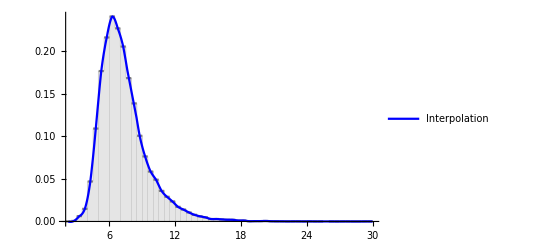

```mathematica
Show[plot6,plotαMCTableInterpamp]
```

```mathematica
αSampleLogamp=Prepend[10^Range[-6,11,0.1],0];
```

```mathematica
fun1αamp[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])];
```

```mathematica
fun1αampTable[y_]=Table[{αSampleLogamp[[i]],fun1αphase[αSampleLogamp[[i]],y]},{i,1,Length[αSampleLogamp]}];
```

```mathematica
αFinalPDFampLog=Table[{fun1αampTable[y][[i,1]],NIntegrate[fun1αampTable[y][[i,2]]αMCTableInterpamp[y],{y,2.25,30}]},{i,1,Length[fun1αampTable[y]]}];
```

```mathematica
αFinalPDFampInterpLog=Interpolation[αFinalPDFampLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationamp=NIntegrate[αFinalPDFampInterpLog[x],{x,0,10^11}]
```

0.499362

```mathematica
αFinalPDFampLogNorm=Table[{αFinalPDFampLog[[i,1]],αFinalPDFampLog[[i,2]]/αNormalizationamp},{i,1,Length[αFinalPDFampLog]}];
```

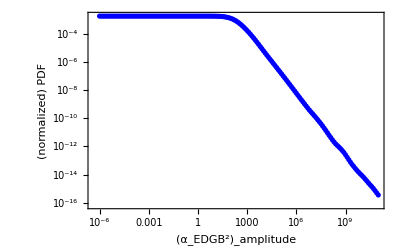

```mathematica
plotαFinalPDFampLogNorm=ListLogLogPlot[{αFinalPDFampLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_amplitude","(normalized) PDF"}]
```

```mathematica
αFinalPDFampInterpLogNorm=Interpolation[αFinalPDFampLogNorm];
```

```mathematica
αFinalCDFampNorm=Table[{αSampleLogamp[[i]],NIntegrate[αFinalPDFampInterpLogNorm[x],{x,0,αSampleLogamp[[i]]}]},{i,1,Length[αSampleLogamp]}];
```

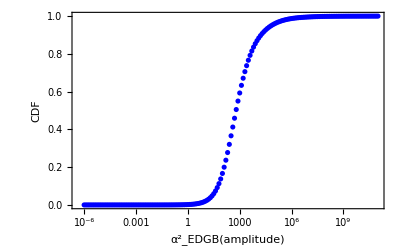

```mathematica
ListLogLinearPlot[αFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB(amplitude)","CDF"}]
```

```mathematica
αFinalCDFampNormInterp=Interpolation[αFinalCDFampNorm];
```

```mathematica
αSquared90CLamp=x/.FindRoot[αFinalCDFampNormInterp[x]==0.9,{x,1000}](*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

16966.5

```mathematica
√√αSquared90CLamp
```

11.413

```mathematica
11.405946092337743
```

11.4059

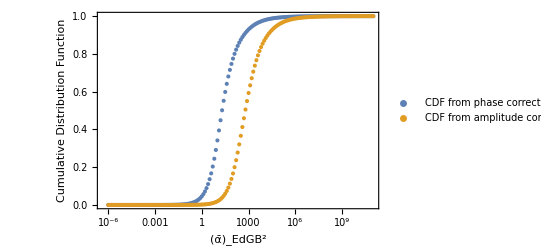

```mathematica
PlotCDFComparison=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm},PlotRange->All,TicksStyle->Directive["Label",14],AxesLabel->{nPN,Subscript[σ, α]},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction"},LabelStyle->{FontSize->5},LegendMarkerSize->10,LegendMargins->0,LegendFunction->"Frame"],{Left,Top}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},Frame->True]
```

## ζ from phase correction

### 2D Gaussian, ζ samples

```mathematica
𝒟log=HistogramDistribution[Log[ζphaseAll]] (*simga_zeta from log of phase correction from monte-carlo. If we use the distribution of ζ, the pdf we get looks almost rectangular. That is why we are using the log[sigma_zeta]. We can compare their shapes from following two histograms *)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζphaseAll]];
```

```mathematica
Histogram[ζphaseAll];
```

```mathematica
ps1=PDF[𝒟log,x];
```

```mathematica
ps2[x]=ps1;
```

```mathematica
plottest2=Plot[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]},Filling->Axis,PlotStyle->Gray,PlotRange->All];
```

```mathematica
zeta1=ListLinePlot[{{0,0},{0,0.25}},PlotStyle->Red];
```

```mathematica
Show[plottest2,zeta1,Frame->True,PlotRange->All] ;(*Shows how much of the area under the curve satisfies zeta<1 from phase correction*)
```

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]
```

0.999836

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],0}]/Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]*100 (*98% area under the curve satisfies zeta<1 from phase correction*)
```

98.2835

```mathematica
MaxLogζphase=Log[Max[ζphaseAll]]
```

15.8769

```mathematica
MinLogζphase=Log[Min[ζphaseAll]]
```

-13.4813

```mathematica
fun1kent[x_,y_]=1/(√(2*π) Exp[y])*Exp[-x^2/(2Exp[2y])]
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

ζ sample

```mathematica
ζSampleLog=Prepend[10^Range[-5,3,0.1],0];
```

Creating a table for fun1Kent[x,y] at each ζ sample for x

```mathematica
fun1TableLog[y_]=Table[{ζSampleLog[[i]],fun1kent[ζSampleLog[[i]],y]},{i,1,Length[ζSampleLog]}];
```

```mathematica
ζMC[x_]=ps1;
```

```mathematica
ζMC[-14.5]
ζMC[16.5]
```

0.

0.

ζ sample for creating an interpolation function for the MC prob distribution
Since ζ > 0, I only consider positive ζ

```mathematica
ζMCSample=Range[-14.5,16.5,1];
```

creating a table for the MC distribution at each sample ζ

```mathematica
ζMCTable=Table[{ζMCSample[[i]],ζMC[ζMCSample[[i]]]},{i,1,Length[ζMCSample]}];
```

creating an interpolation function

```mathematica
ζMCTableInterp=Interpolation[ζMCTable];
```

Plot

```mathematica
plotζMCTableInterp=Plot[ζMCTableInterp[x],{x,-14.5,16.5},PlotStyle->Blue,PlotLegends->{"Interpolation"}];
```

Comparison with the actual distribution

```mathematica
Show[plotζMCTableInterp,plottest2,Frame->True,FrameLabel->{"Log σ_ζ","PDF"}];
```

```mathematica
ζFinalPDFPhaseLog=Table[{fun1TableLog[y][[i,1]],NIntegrate[fun1TableLog[y][[i,2]]ζMCTableInterp[y],{y,MinLogζphase,MaxLogζphase}]},{i,1,Length[fun1TableLog[y]]}];
```

#### Normalized Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLog=Interpolation[ζFinalPDFPhaseLog];
```

Normalization

```mathematica
Normalization=NIntegrate[ζFinalPDFPhaseInterpLog[x],{x,0,1000}]
```

0.498985

Normalized distribution

```mathematica
ζFinalPDFPhaseLogNorm=Table[{ζFinalPDFPhaseLog[[i,1]],ζFinalPDFPhaseLog[[i,2]]/Normalization},{i,1,Length[ζFinalPDFPhaseLog]}];
```

Plot

```mathematica
plotζFinalPDFPhaseLogNorm=ListLogLogPlot[{ζFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ","(normalized) PDF"}];
```

#### Cumulative Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLogNorm=Interpolation[ζFinalPDFPhaseLogNorm];
```

Creating a table for cumulative distribution

```mathematica
ζFinalCDFPhaseNorm=Table[{ζSampleLog[[i]],NIntegrate[ζFinalPDFPhaseInterpLogNorm[x],{x,0,ζSampleLog[[i]]}]},{i,1,Length[ζSampleLog]}];
```

Plot

```mathematica
ListLogLinearPlot[ζFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}];
```

CDF nicely asymptotes to 1 (suggesting that ζ = 100 is large enough)

#### Finding 90% credible limit for ζ

Interpolation for CDF

```mathematica
ζFinalCDFPhaseNormInterp=Interpolation[ζFinalCDFPhaseNorm];
```

90% limit

```mathematica
ζ90CLphase=x/.FindRoot[ζFinalCDFPhaseNormInterp[x]==0.9,{x,0.02}]
```

0.0205204

```mathematica
ζ  from amplitude correction
```

amplitude correction from ζ

```mathematica
𝒟logamp=HistogramDistribution[Log[ζampAll]] (*zeta from log of amp correction from monte-carlo*)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζampAll]];
```

```mathematica
Histogram[ζampAll];
```

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
MinLogζamp=Min[Log[ζampAll]]
```

-10.7176

```mathematica
MaxLogζamp=Max[Log[ζampAll]]
```

19.4335

```mathematica
plottestamp=Plot[ps2amp[x],{x,-10,20},Filling->Axis,PlotStyle->Gray];
```

```mathematica
Show[plottestamp,zeta1,Frame->True] ;(*Shows how much of the area under the curve satisfies zeta<1 from amplitude correction*)
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]
```

0.9998

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],0}]/Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]*100 (*89.7% area under the curve satisfies zeta<1 from amplitude correction*)
```

89.7039

```mathematica
ζSampleLogamp=Prepend[10^Range[-5,3,0.1],0];
```

```mathematica
fun1TableLogamp[y_]=Table[{ζSampleLogamp[[i]],fun1kent[ζSampleLogamp[[i]],y]},{i,1,Length[ζSampleLogamp]}];
```

```mathematica
ζMCamp[x_]=ps1amp;
```

```mathematica
ζMCamp[-11.5]
ζMCamp[20]
```

0.

0.

```mathematica
ζMCSampleamp=Range[-11.5,20,1];
```

```mathematica
ζMCTableamp=Table[{ζMCSampleamp[[i]],ζMCamp[ζMCSampleamp[[i]]]},{i,1,Length[ζMCSampleamp]}];
```

```mathematica
ζMCTableInterpamp=Interpolation[ζMCTableamp];
```

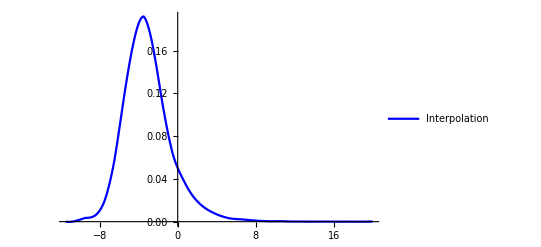

```mathematica
plotζMCTableInterpamp=Plot[ζMCTableInterpamp[x],{x,-11.5,20},PlotStyle->Blue,PlotLegends->{"Interpolation"}]
```

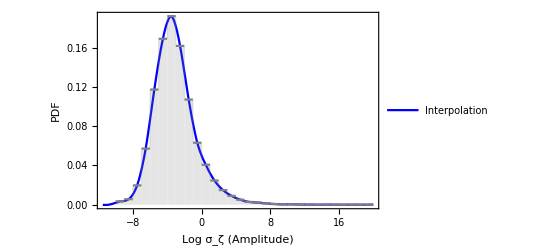

```mathematica
Show[plotζMCTableInterpamp,plottestamp,Frame->True,FrameLabel->{"Log σ_ζ (Amplitude)","PDF"}]
```

```mathematica
ζFinalPDFampLog=Table[{fun1TableLogamp[y][[i,1]],NIntegrate[fun1TableLogamp[y][[i,2]]ζMCTableInterpamp[y],{y,MinLogζamp,MaxLogζamp}]},{i,1,Length[fun1TableLogamp[y]]}];
```

```mathematica
ζFinalPDFampInterpLog=Interpolation[ζFinalPDFampLog];
```

Normalization

```mathematica
Normalizationζamp=NIntegrate[ζFinalPDFampInterpLog[x],{x,0,1000}]
```

0.497949

```mathematica
ζFinalPDFampLogNorm=Table[{ζFinalPDFampLog[[i,1]],ζFinalPDFampLog[[i,2]]/Normalizationζamp},{i,1,Length[ζFinalPDFampLog]}];
```

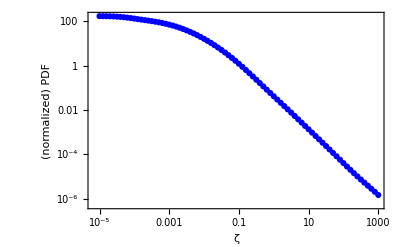

```mathematica
plotζFinalPDFampLogNorm=ListLogLogPlot[{ζFinalPDFampLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ","(normalized) PDF"}]
```

```mathematica
ζFinalPDFampInterpLogNorm=Interpolation[ζFinalPDFampLogNorm];
```

```mathematica
ζFinalCDFampNorm=Table[{ζSampleLogamp[[i]],NIntegrate[ζFinalPDFampInterpLogNorm[x],{x,0,ζSampleLogamp[[i]]}]},{i,1,Length[ζSampleLogamp]}];
```

```mathematica
ListLogLinearPlot[ζFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}];
```

```mathematica
ζFinalCDFampNormInterp=Interpolation[ζFinalCDFampNorm];
```

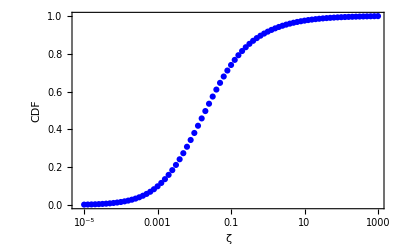

```mathematica
ListLogLinearPlot[ζFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}]
```

```mathematica
ζ90CLamp=x/.FindRoot[ζFinalCDFampNormInterp[x]==0.9,{x,0.02}]
```

0.676947

```mathematica
Combining the upper bounds on ζ from phase and amplitude corrections:
```